```mathematica
(*MSH=np.exp(np.random.normal(np.log(mu),np.log(sigma),N_spots))
(* MSH (area) to R_star (length) converter. Conversion from
'On Sunspot and Starspot Lifetimes'-https://arxiv.org/pdf/1409.4337.pdf*)
sizes=np.sqrt(micro_solar_hemispheres*17682025)/695500.0*)
```

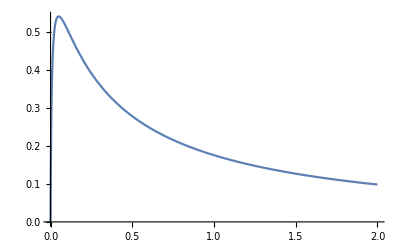

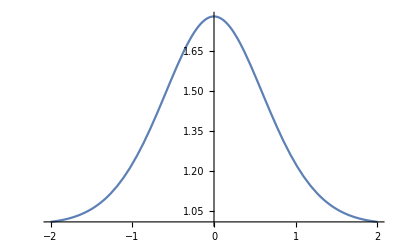

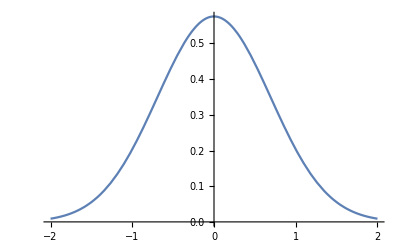

```mathematica
Plot[PDF[LogNormalDistribution[1,2],x], {x,0,2}]
Plot[Exp[PDF[NormalDistribution[Log[1],Log[2]],x]], {x,-2,2}]
Plot[PDF[NormalDistribution[Log[1],Log[2]],x], {x,-2,2}]
```

```mathematica
μ=11.8; σ=2.55;
list = {FullSimplify[PDF[NormalDistribution[μ,σ],x]],
FullSimplify[PDF[NormalDistribution[Log[μ],Log[σ]],x]],
FullSimplify[Exp[PDF[NormalDistribution[Log[μ],Log[σ]],x]]],
FullSimplify[PDF[LogNormalDistribution[μ,σ],x]],
FullSimplify[PDF[LogNormalDistribution[Log[μ],Log[σ]],x]]}
```

{0.156448 ⅇ^(-0.0768935 (-11.8+x)^2),0.426178 ⅇ^(-0.5706 (-2.4681+x)^2),ⅇ^(0.426178 ⅇ^(-0.5706 (-2.4681+x)^2)),Piecewise[{{3.50373×10^-6 ⅇ^(-0.0768935 Log[x]^2) x^0.814687, x>0}, {0, True}}],Piecewise[{{0.0131845 ⅇ^(-0.5706 Log[x]^2) x^1.81659, x>0}, {0, True}}]}

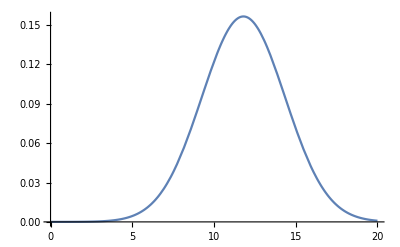
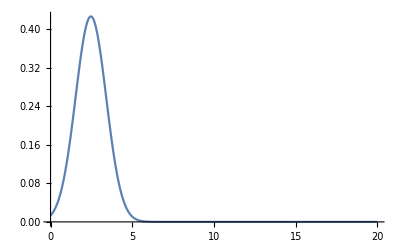
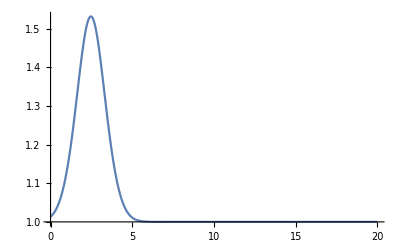
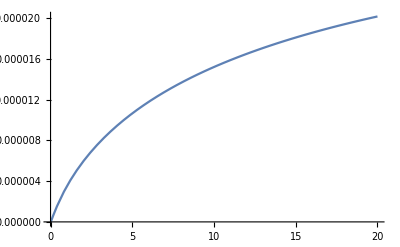
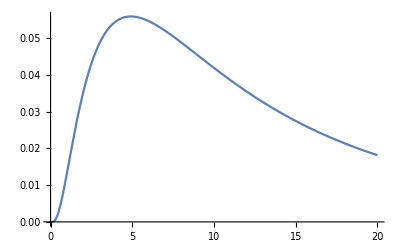

```mathematica
Table[Plot[list[[i]],{x,0,20},PlotRange->Full],{i,1,5}]
```

```mathematica
NormalDistribution[Log[μ],Log[σ]]
```

NormalDistribution[2.4681,0.936093]

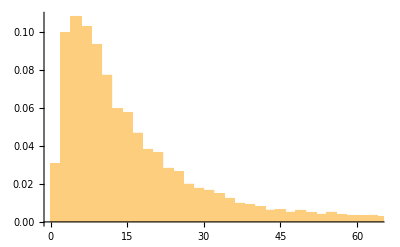

```mathematica
Histogram[Exp[RandomVariate[NormalDistribution[Log[μ],Log[σ]],10000]],Automatic,"Probability"]
```

```mathematica
test = HistogramList[RandomVariate[LogNormalDistribution[Log[μ],Log[σ]],10000],Automatic,"Probability"];
testx=test[[1,Range[2,30]]]
testy=test[[2,Range[2,30]]]
ListLogLogPlot[testx,testy]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58}

{0.0957,0.1131,0.1041,0.0911,0.0742,0.0662,0.0564,0.0441,0.0386,0.0338,0.0279,0.0278,0.0208,0.0179,0.019,0.0142,0.0117,0.0105,0.0114,0.0072,0.0072,0.0054,0.0058,0.006,0.0042,0.0041,0.0029,0.0041,0.0024}

ListLogLogPlot::nonopt: Options expected (instead of {0.0957,0.1131,0.1041,0.0911,0.0742,0.0662,0.0564,0.0441,0.0386,0.0338,0.0279,0.0278,0.0208,0.0179,0.019,0.0142,0.0117,0.0105,0.0114,0.0072,0.0072,0.0054,0.0058,0.006,0.0042,0.0041,0.0029,0.0041,0.0024}) beyond position 1 in ListLogLogPlot[{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58},{0.0957,0.1131,0.1041,0.0911,0.0742,0.0662,0.0564,0.0441,0.0386,0.0338,0.0279,0.0278,0.0208,«3»,0.0117,0.0105,0.0114,0.0072,0.0072,0.0054,0.0058,0.006,0.0042,0.0041,0.0029,0.0041,0.0024}]. An option must be a rule or a list of rules.

ListLogLogPlot[{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58},{0.0957,0.1131,0.1041,0.0911,0.0742,0.0662,0.0564,0.0441,0.0386,0.0338,0.0279,0.0278,0.0208,0.0179,0.019,0.0142,0.0117,0.0105,0.0114,0.0072,0.0072,0.0054,0.0058,0.006,0.0042,0.0041,0.0029,0.0041,0.0024}]